## Analysis of the SAIR using the RN:

```mathematica
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];
AppendTo[$Path, FileNameJoin[{$HomeDirectory, "Dropbox", "Codes"}]];
SystemOpen[FileNameJoin[{$HomeDirectory, "Kernel", "EpidCRN.m"}]];

<<EpidCRN`;
(*?EpidCRN`* *)
Needs["ReactionKinetics`"];

Format[γr]:=Subscript[γ,r];Format[be]:=Subscript[β,e];Format[μi]:=Subscript[μ,i];
Format[γs]:=Subscript[γ,s]; Format[ge]:=Subscript[γ,e]; Format[bi]:=Subscript[β,i];
Format[γi]:=Subscript[γ,i];Format[La]=Λ;
clm={La->μ};
R0=((γr+μ) (ai bi+be (γi+δ+μ)))/((ai+ar+μ) (γr+γs+μ) (γi+δ+μ));mR=(ai bi+be (γi+δ+μ))/((ai+ar+μ)  (γi+δ+μ));


(*cai={ai->ge-ar};cga={ge->ai+ar};*) cr={r->1-s-a-i};
RN={"0"->"S","S"+"A"->2 "A", "S"+"I"-> "I"+"A","A"->"I","A"->"R","S"->"R","I"->"R","R"->"I",
"S"->"0","A"->"0","I"->"0","R"->"0"};
var={s,e,i,r};
RND=ReactionsData[RN];
S= RND["γ"]//Normal;
expo= RND["α"]//Normal//Transpose;
{comp,reac,nR,spec,nS,vol,vars,defi}=RND["complexes","reactionsteps","R","species","M","volpertgraph",
"variables","deficiency"];
fl=cons[S//Transpose]//Transpose;
```

```mathematica
rv=expM[var,expo];(*monomial part of rates*)
tra={La  ,be  ,bi ,ai,ar,γs ,γi ,γr ,μ ,μ ,μ+δ ,μ };
(*par with SM order, and some repetitions, used in defining Rv*)
Rv=tra*rv/.clm;(*rates*)

RHS=S.Rv//Simplify; jac=Grad[RHS,var];
par=Par[RHS,var];cp=Thread[par>0];
Print["SAIR model  ",RHS//MatrixForm," has ", par//Length,
" par : ", par]
Print["The SAIR  Stochiometric repr ",Row[{S//MatrixForm,Rv}]," has rank ",MatrixRank[S],
"  deficiency ", defi, 
" and ",comp//Length," complexes and ",fl//Length,"  fluxes"]
```

ReactionKinetics Version 1.0 [March 25, 2018] using Mathematica Version 13.3.0 for Microsoft Windows (64-bit) (June 3, 2023) (Version 13.3, Release 0) loaded 26 February 2025 at 10:34 TimeZone
GNU General Public License (GPLv3) Terms Apply.

Please report any issues, comments, complaint related to ReactionKinetics at
[jtoth@math.bme.hu](mailto:jtoth@math.bme.hu), [nagyal@math.bme.hu](mailto:nagyal@math.bme.hu) or [dpapp@iems.northwestern.edu](mailto:dpapp@iems.northwestern.edu)

SAIR model  (-β_e e s-β_i i s-s γ_s+μ-s μ
-ai e-ar e+β_e e s+β_i i s-e μ
ai e+r γ_r-i (γ_i+δ+μ)
ar e+i γ_i-r γ_r+s γ_s-r μ) has 9 par : {ai,ar,β_e,β_i,γ_i,γ_r,γ_s,δ,μ}

The SAIR  Stochiometric repr (1 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | -1){μ,β_e e s,β_i i s,ai e,ar e,s γ_s,i γ_i,r γ_r,s μ,e μ,i (δ+μ),r μ} has rank 4  deficiency δ=N-L-S=9-3-4=2 and 9 complexes and 12  fluxes

```mathematica
so=Solve[RHS==0,var]//FullSimplify;
Print["The  ", so//Length,"fixed points are"]
so
 Print["Check sum ",Total[RHS]//FullSimplify,"  cdfe is ", cdfe=so[[1]],s+a+i+r/.so[[2]]//FullSimplify]
 
 jac=Grad[RHS,var]//FullSimplify;
chEq=Det[ϵ IdentityMatrix[4]-jac]//Factor;
ch0= chEq/.so[[1]]//Factor;
chE= chEq/.so[[2]]//Factor;
Print["Jacobian at DFE",jac/.cdfe//MatrixForm," does not have block form, but chEq has two trivial 
factors ",chEq/.cdfe//Factor]
```

ReactionKinetics Version 1.0 [March 25, 2018] using Mathematica Version 13.3.0 for Microsoft Windows (64-bit) (June 3, 2023) (Version 13.3, Release 0) loaded 26 February 2025 at 10:31 TimeZone
GNU General Public License (GPLv3) Terms Apply.

Please report any issues, comments, complaint related to ReactionKinetics at
[jtoth@math.bme.hu](mailto:jtoth@math.bme.hu), [nagyal@math.bme.hu](mailto:nagyal@math.bme.hu) or [dpapp@iems.northwestern.edu](mailto:dpapp@iems.northwestern.edu)

SAIR model  (-β_a e s-β_i i s-s γ_s+μ-s μ
-ai e-ar e+β_a e s+β_i i s-e μ
ai e+r γ_r-i (γ_i+δ+μ)
ar e+i γ_i-r γ_r+s γ_s-r μ) has 9 par : {ai,ar,β_a,β_i,γ_i,γ_r,γ_s,δ,μ}

The SAIR  Stochiometric repr (1 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | -1 | 0 | 0 | 0 | -1){μ,β_a e s,β_i i s,ai e,ar e,s γ_s,i γ_i,r γ_r,s μ,e μ,i (δ+μ),r μ} has rank 4  deficiency δ=N-L-S=9-3-4=2 and 9 complexes and 12  fluxes

### Computation of Jy, its principal eigenvectors, and R0 using NGM script, and the check of the positivity of the endemic point:

```mathematica
mod={RHS,var,par};
inf={2,3};
Print["(a'
i')=", RHS[[inf]]//MatrixForm]
jacI=Grad[RHS[[inf]],var[[inf]]]; jac=Grad[RHS,var]//FullSimplify;
ng=NGM[mod,inf];K=ng[[6]];M=ng[[1]];
Tm=ng[[5]];
F=ng[[4]];
Print["M is",M//MatrixForm, " and K=",K//MatrixForm," has eig"]
eig=K//Eigenvalues
R0=eig[[2]]/.cdfe//FullSimplify;
Print["R0=",R0]
va={1,0};
bb={be,bi};
reiv=Inverse[-Tm].va//FullSimplify;
leiv=bb.Inverse[-Tm]//FullSimplify;
Print["A=",Tm//MatrixForm,"dwell times=",reiv,"C=eiv=",leiv]
Print["check:M .reiv(leiv) are",M.reiv/.s->1/mR//Factor,leiv.M/.s->1/mR//Factor]


jacE=(jacI/.s->1/mR)//FullSimplify;
eigE=Eigenvalues[jacE]//FullSimplify;
Print["infectious Jacobian at EE:",jacE//MatrixForm, "  its eigs are",  eigE]
aH=va .Inverse[s IdentityMatrix[2]+Transpose[ng[[5]]]].bb;
Print["The LT of the total force of infection  is â(s)=", aH, " and R =â(0)=", aH/.s->0//FullSimplify]
{ae,ie}={a,i}/.so[[2]]//FullSimplify
Print["The quotient of endemic a*/i* is ", aovi=ae/ie//FullSimplify]
```

(a'
i')=(β_i i s-a (a_i+a_r-β_a s+μ)
a a_i-i (γ_i+δ+μ))

M is(-a_i-a_r+β_a s-μ | β_i s
a_i | -γ_i-δ-μ) and K=((s (a_i β_i+β_a (γ_i+δ+μ)))/((a_i+a_r+μ) (γ_i+δ+μ)) | (β_i s)/(γ_i+δ+μ)
0 | 0) has eig

{0,(s (a_i β_i+β_a γ_i+β_a δ+β_a μ))/((a_i+a_r+μ) (γ_i+δ+μ))}

R0=((γ_r+μ) (a_i β_i+β_a (γ_i+δ+μ)))/((a_i+a_r+μ) (γ_r+γ_s+μ) (γ_i+δ+μ))

A=(-a_i-a_r-μ | 0
a_i | -γ_i-δ-μ)dwell times={1/(a_i+a_r+μ),a_i/((a_i+a_r+μ) (γ_i+δ+μ))}C=eiv={(a_i β_i+β_a (γ_i+δ+μ))/((a_i+a_r+μ) (γ_i+δ+μ)),β_i/(γ_i+δ+μ)}

check:M .reiv(leiv) are{0,0}{0,0}

infectious Jacobian at EE:(-(a_i β_i (a_i+a_r+μ))/(a_i β_i+β_a (γ_i+δ+μ)) | (β_i (a_i+a_r+μ) (γ_i+δ+μ))/(a_i β_i+β_a (γ_i+δ+μ))
a_i | -γ_i-δ-μ)  its eigs are{0,-(a_i^2 β_i+β_a (γ_i+δ+μ)^2+a_i β_i (a_r+γ_i+δ+2 μ))/(a_i β_i+β_a (γ_i+δ+μ))}

The LT of the total force of infection  is â(s)=β_a/(-a_i-a_r+s-μ)-(a_i β_i)/((-a_i-a_r+s-μ) (s-γ_i-δ-μ)) and R =â(0)=-(a_i β_i+β_a (γ_i+δ+μ))/((a_i+a_r+μ) (γ_i+δ+μ))

{-((μ (γ_i+δ+μ) ((γ_i+δ+μ) (-β_a (γ_r+μ)+a_r (γ_r+γ_s+μ)+μ (γ_r+γ_s+μ))+a_i (-β_i (γ_r+μ)+(γ_r+γ_s+μ) (γ_i+δ+μ))))/((a_i β_i+β_a (γ_i+δ+μ)) (a_i γ_i μ+a_i (γ_r+μ) (δ+μ)+μ (a_r+γ_r+μ) (γ_i+δ+μ)))),(a_i μ (-((γ_i+δ+μ) (-β_a (γ_r+μ)+a_r (γ_r+γ_s+μ)+μ (γ_r+γ_s+μ)))+a_i (β_i (γ_r+μ)-(γ_r+γ_s+μ) (γ_i+δ+μ))))/((a_i β_i+β_a (γ_i+δ+μ)) (a_i γ_i μ+a_i (γ_r+μ) (δ+μ)+μ (a_r+γ_r+μ) (γ_i+δ+μ)))}

The quotient of endemic a,i is (γ_i+δ+μ)/a_i

```mathematica
(*Total and Lie derivative *)
 Lf=leiv.{a-ae Log[a],i-ie Log[a]}/.s->1/mR;
Td=Dt[Lf, t, Constants -> par];(*Total  derivative *)
rules = {Dt[a,t,Constants->par] -> RHS[[2]], Dt[i,t,Constants->par] ->RHS[[3]]};
Ld=Td//.rules//.s->1/mR//Factor
R0
```

-((β_i μ (-a a_i+i γ_i+i δ+i μ) (a_i^2 β_i+a_i a_r β_i+a_i β_i γ_i+β_a γ_i^2+a_i β_i δ+2 β_a γ_i δ+β_a δ^2+2 a_i β_i μ+2 β_a γ_i μ+2 β_a δ μ+β_a μ^2) (a_i β_i γ_r-a_i γ_i γ_r-a_r γ_i γ_r+β_a γ_i γ_r-a_i γ_i γ_s-a_r γ_i γ_s-a_i γ_r δ-a_r γ_r δ+β_a γ_r δ-a_i γ_s δ-a_r γ_s δ+a_i β_i μ-a_i γ_i μ-a_r γ_i μ+β_a γ_i μ-a_i γ_r μ-a_r γ_r μ+β_a γ_r μ-γ_i γ_r μ-a_i γ_s μ-a_r γ_s μ-γ_i γ_s μ-a_i δ μ-a_r δ μ+β_a δ μ-γ_r δ μ-γ_s δ μ-a_i μ^2-a_r μ^2+β_a μ^2-γ_i μ^2-γ_r μ^2-γ_s μ^2-δ μ^2-μ^3))/(a (γ_i+δ+μ) (a_i β_i+β_a γ_i+β_a δ+β_a μ)^2 (a_i γ_r δ+a_i γ_i μ+a_r γ_i μ+a_i γ_r μ+γ_i γ_r μ+a_i δ μ+a_r δ μ+γ_r δ μ+a_i μ^2+a_r μ^2+γ_i μ^2+γ_r μ^2+δ μ^2+μ^3)))

((γ_r+μ) (a_i β_i+β_a (γ_i+δ+μ)))/((a_i+a_r+μ) (γ_r+γ_s+μ) (γ_i+δ+μ))

```mathematica
nLd=Numerator[Ld];nLd//Length
va=Variables[nLd]
Exponent[nLd,va]
Exponent[nLd,{a,i}]
fi=FindInstance[Append[Join[cp,{a>0,i>0,R0>1}],nLd>0],va]
nLd/.fi//N
```

6

```mathematica
{bi,μ,a,ai,i,γi,δ,ar,be,γr,γs}
```

{3,7,1,4,1,4,4,2,2,1,1}

{1,1}

```mathematica
{{bi->11,μ->1,a->4,ai->1,i->1,γi->1,δ->1,ar->1,be->1,γr->1,γs->1}}
```

{825.}

```mathematica
Jdd=Numerator[Together[Det[jac/.dfe]]//FullSimplify];Print["Det[jac/.dfe]=", Jdd]
Print["Det[M/.dfe]=", Det[M/.dfe]//FullSimplify]
Jed=Numerator[Together[Det[jac/.so[[2]]]]]//FullSimplify;
Print["Det[jac/.E*]=", Jed]
rd=Reduce[Append[cp,Jdd==0]]//FullSimplify
re=Reduce[Append[cp,Jed==0]]//FullSimplify
Print["Jed and Jdd are opposites, their sum is"]
Jdd+Jed
(*Print["Det[M/.E*]=", Det[M/.so[[2]]]//FullSimplify]

Print["eigenvalues of M at endemic point are ", Eigenvalues[M/.so[[2]]]//FullSimplify]
Print["eigenvalues of M at E0 are ", Eigenvalues[M/.dfe]//FullSimplify]*)
```

Det[jac/.dfe]=μ ((γ_i+μ) (-β_a (γ_r+μ)+a_r (γ_r+γ_s+μ)+μ (γ_r+γ_s+μ))+a_i (-β_i (γ_r+μ)+(γ_i+μ) (γ_r+γ_s+μ)))

Det[M/.dfe]=((γ_i+μ) (-β_a (γ_r+μ)+a_r (γ_r+γ_s+μ)+μ (γ_r+γ_s+μ))+a_i (-β_i (γ_r+μ)+(γ_i+μ) (γ_r+γ_s+μ)))/(γ_r+γ_s+μ)

Det[jac/.E*]=-μ ((γ_i+μ) (-β_a (γ_r+μ)+a_r (γ_r+γ_s+μ)+μ (γ_r+γ_s+μ))+a_i (-β_i (γ_r+μ)+(γ_i+μ) (γ_r+γ_s+μ)))

```mathematica
(ai>0&&Subscript[γ, r]>0&&γs>0&&μ>0&&be>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar+μ==(be (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ)&&γi>0&&bi==((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ))||(μ>0&&Subscript[γ, r]>0&&γs>0&&γi>0&&((0<bi<((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&be>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar>0&&ar+μ<(be (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ))||(bi>((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&((0<be≤(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar>0)||(be>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar+μ>(be (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ)))))&&ai==((γi+μ) (-be (Subscript[γ, r]+μ)+ar (Subscript[γ, r]+γs+μ)+μ (Subscript[γ, r]+γs+μ)))/(bi (Subscript[γ, r]+μ)-(γi+μ) (Subscript[γ, r]+γs+μ)))
```

```mathematica
(ai>0&&Subscript[γ, r]>0&&γs>0&&μ>0&&be>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar+μ==(be (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ)&&γi>0&&bi==((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ))||(μ>0&&Subscript[γ, r]>0&&γs>0&&γi>0&&((0<bi<((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&be>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar>0&&ar+μ<(be (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ))||(bi>((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&((0<be≤(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar>0)||(be>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar+μ>(be (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ)))))&&ai==((γi+μ) (-be (Subscript[γ, r]+μ)+ar (Subscript[γ, r]+γs+μ)+μ (Subscript[γ, r]+γs+μ)))/(bi (Subscript[γ, r]+μ)-(γi+μ) (Subscript[γ, r]+γs+μ)))
```

Jed and Jdd are opposites, their sum is

0

```mathematica
cgs={γs->vs-μ -γr}; cge={ar->ve-μ -ai}; cg={γi->vi-μ -δ};cgr={γr->(vr-(ve+γr)vi)/ai};
con=Join[cgs,cge,cg];
Print["a endemic in terms of v's: "]
enda=a/.so[[2]]//.cgs//.cg//.cge//FullSimplify
Print["1-1/R0 =", Together[(1-1/R0)//.cgs//.cg//.cge]]

Print["where R0=", R0//.con//FullSimplify]
```

a endemic in terms of v's:

```mathematica
((vi-δ) (ve vs (-vi+δ)+(vi be+ai bi-be δ) (Subscript[γ, r]+μ)))/((ai Subscript[γ, r]+(ve+Subscript[γ, r]) (vi-δ)) (vi be+ai bi-be δ))
```

1-1/R0 =(-ve vi vs+vi β_a γ_r+a_i β_i γ_r+ve vs δ-β_a γ_r δ+vi β_a μ+a_i β_i μ-β_a δ μ)/((vi β_a+a_i β_i-β_a δ) (γ_r+μ))

where R0=((vi β_a+a_i β_i-β_a δ) (γ_r+μ))/(ve vs (vi-δ))

```mathematica
re=r/.so[[2]]//.cgs//.cg//.cge/.δ->0//FullSimplify
Together[(R-1)//.cgs//.cg//.cge]
1/R//.cgs//.cg//.cge
```

```mathematica
(ve vi (vi (-ve+vs+be-Subscript[γ, r])+ai (vs+bi-Subscript[γ, r]))-(ai+vi) (vi be+ai bi) μ)/((vi be+ai bi) (ve vi+(ai+vi) Subscript[γ, r]))
```

```mathematica
(-ve vi+vi be+ai bi)/(ve vi)
```

```mathematica
(ve vi)/(vi be+ai bi)
```

```mathematica
Reduce[Join[cp,Thread[Drop[Eigenvalues[jac/.dfe]//FullSimplify,2]<0],{R0>1}]]
Reduce[Join[cp,Thread[Drop[Eigenvalues[jac/.dfe]//FullSimplify,2]<0]]]
```

False

```mathematica
μ>0&&γi>0&&Subscript[γ, r]>0&&γs>0&&((0<be≤(Subscript[γ, r] μ+γs μ+μ^2)/(Subscript[γ, r]+μ)&&ar>0&&ai>0&&0<bi<1/(ai Subscript[γ, r]+ai μ)(ai γi Subscript[γ, r]+ar γi Subscript[γ, r]-be γi Subscript[γ, r]+ai γi γs+ar γi γs+ai γi μ+ar γi μ-be γi μ+ai Subscript[γ, r] μ+ar Subscript[γ, r] μ-be Subscript[γ, r] μ+γi Subscript[γ, r] μ+ai γs μ+ar γs μ+γi γs μ+ai μ^2+ar μ^2-be μ^2+γi μ^2+Subscript[γ, r] μ^2+γs μ^2+μ^3))||(be>(Subscript[γ, r] μ+γs μ+μ^2)/(Subscript[γ, r]+μ)&&((0<ar<(be Subscript[γ, r]+be μ-Subscript[γ, r] μ-γs μ-μ^2)/(Subscript[γ, r]+γs+μ)&&ai>(-ar Subscript[γ, r]+be Subscript[γ, r]-ar γs-ar μ+be μ-Subscript[γ, r] μ-γs μ-μ^2)/(Subscript[γ, r]+γs+μ)&&0<bi<1/(ai Subscript[γ, r]+ai μ)(ai γi Subscript[γ, r]+ar γi Subscript[γ, r]-be γi Subscript[γ, r]+ai γi γs+ar γi γs+ai γi μ+ar γi μ-be γi μ+ai Subscript[γ, r] μ+ar Subscript[γ, r] μ-be Subscript[γ, r] μ+γi Subscript[γ, r] μ+ai γs μ+ar γs μ+γi γs μ+ai μ^2+ar μ^2-be μ^2+γi μ^2+Subscript[γ, r] μ^2+γs μ^2+μ^3))||(ar≥(be Subscript[γ, r]+be μ-Subscript[γ, r] μ-γs μ-μ^2)/(Subscript[γ, r]+γs+μ)&&ai>0&&0<bi<1/(ai Subscript[γ, r]+ai μ)(ai γi Subscript[γ, r]+ar γi Subscript[γ, r]-be γi Subscript[γ, r]+ai γi γs+ar γi γs+ai γi μ+ar γi μ-be γi μ+ai Subscript[γ, r] μ+ar Subscript[γ, r] μ-be Subscript[γ, r] μ+γi Subscript[γ, r] μ+ai γs μ+ar γs μ+γi γs μ+ai μ^2+ar μ^2-be μ^2+γi μ^2+Subscript[γ, r] μ^2+γs μ^2+μ^3)))))
```

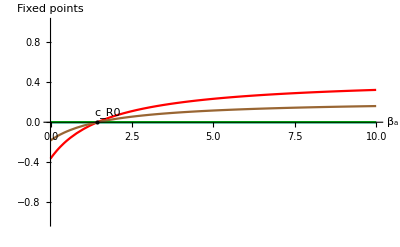

```mathematica
(*Some tests*)
fin=FindInstance[Join[cp,Thread[(var/.so[[2]])>0]],par][[1]];
cN=Drop[fin,{3}];cR0=par[[3]]/.Solve[R0==1,par[[3]]][[1]]; cR0N=cR0/.cN;
fpB=Bifp[mod,cN,inf,par[[3]],0,10,-1,1,cR0N];
fpB[[2]]
```

### Analysis of 3-dim model:

```mathematica
RHS3=Drop[RHS/.cr,-1];//FullSimplify
Print["The 3dim model is", RHS3//MatrixForm]
```

The 3dim model is(-a s β_a-i s β_i+(1-a-i-s) γ_r-s γ_s+Λ-s Λ
i s β_i-a (a_i+a_r-s β_a+Λ)
a a_i-i (γ_i+Λ))

## FHJ graph of SAIR:

In the following we produce the FHJ graph:

```mathematica
groups={{comp[[-1]],comp[[-2]],comp[[-3]],comp[[2]]},{comp[[3]],comp[[4]],comp[[5]],comp[[6]]},{comp[[1]]}}
flow=FHJ[comp,RN,Rv,.5,groups]
Export["SAIRS1gr.pdf",flow]
```

{{R,I,A,S},{A+S,2 A,I+S,A+I},{0}}

SAIRS1gr.pdf

```mathematica
A=Array[a,{2,2}];Ai=Inverse[A];B=Ai.DiagonalMatrix[Array[b,{2}]].A-k IdentityMatrix[2]//Factor;
B//MatrixForm
```

(-(-k a[1,2] a[2,1]+k a[1,1] a[2,2]-a[1,1] a[2,2] b[1]+a[1,2] a[2,1] b[2])/(-a[1,2] a[2,1]+a[1,1] a[2,2]) | -(a[1,2] a[2,2] (b[1]-b[2]))/(a[1,2] a[2,1]-a[1,1] a[2,2])
-(a[1,1] a[2,1] (b[1]-b[2]))/(-a[1,2] a[2,1]+a[1,1] a[2,2]) | -(k a[1,2] a[2,1]-k a[1,1] a[2,2]-a[1,2] a[2,1] b[1]+a[1,1] a[2,2] b[2])/(a[1,2] a[2,1]-a[1,1] a[2,2]))

```mathematica
Print["In the following we dissect the expression of r in order to check its form wrt R0 and check its positivity"]
 nr=Numerator[r/.so[[2]]]; dr=Denominator[r/.so[[2]]];
 Print["the numerator of endemic r is ", nr]
  Print["the Denominator of endemic r is ",dr//FullSimplify]
Print["1-1/R0= ",Together[(1-1/R0)]//FullSimplify]
 (*a check; we already know that the endemic point doesn't exist when R0<1
 Reduce[Join[Thread[(var/.so[[2]])>0],cp,{R0<1}]]*)
```

```mathematica
(*Define Lf as before*)Lf=leiv.{a-ae Log[a],i-ie Log[a]};

(*Define the system dynamics*)
rules={a'[t]->a[t] a[t],i'[t]->i[t] i[t]};  (*Given a'=a a and i'=i i*)

(*Compute the Lie derivative*)
LieDerivative=Dt[Lf,t]/. rules
Lf[a_,i_]:=leiv.{a-ae Log[a],i-ie Log[a]};
LieDerivative=D[Lf[a[t],i[t]],t]/. {a'[t]->a[t] a[t],i'[t]->i[t] i[t]}
```